### Payoff

```mathematica
P1=(cr(n1+1))/n-c-T+ nT/(n1+1) - b ;
```

```mathematica
P2=(cr*n1)/n - β*n3 - T;
```

```mathematica
P3=(cr*n1)/n - M -T + (b*n1)/(n3+1);
```

```mathematica
P={P1,P2,P3};
```

### Expected Payoffs

```mathematica
EP1 = (c*r(x(n-1)+1))/n -c-T-b +T*(1-(1-x)^(n))/x
EP2 =(c*r(n-1)*x)/n- β*z(n-1)-T
EP3 =(c*r(n-1)*x)/n-M-T+ b* x*(1-(1-z)^(n-1))/z
```

-b-c-T+(T (1-(1-x)^n))/x+(c r (1+(-1+n) x))/n

-T+(c (-1+n) r x)/n-(-1+n) z β

-M-T+(c (-1+n) r x)/n+(b x (1-(1-z)^(-1+n)))/z

```mathematica
EP = {EP1, EP2, EP3};
```

```mathematica
{-b-(c (n-r))/n-T+(T (1-(1-x)^n))/x+(c r (1+(-1+n) x))/n,-T+(c (-1+n) r x)/n-(-1+n) z β,-M-T+(c (-1+n) r x)/n+(b x (1-(1-z)^(-1+n)))/z}
```

{-b-(c (n-r))/n-T+(T (1-(1-x)^n))/x+(c r (1+(-1+n) x))/n,-T+(c (-1+n) r x)/n-(-1+n) z β,-M-T+(c (-1+n) r x)/n+(b x (1-(1-z)^(-1+n)))/z}

### Replicator Equations

#### Average Payoff

```mathematica
AP = EP . {x, y, z};
```

#### Replicator Equations

```mathematica
re1=x(EP1-AP);
```

```mathematica
re2=y(EP2-AP)/.x->x/.y->y/.z->1-x-y//Simplify
```

-1/(n (x+y))y (c r x (x+y)+M n (x^2+(-1+y) y+x (-1+2 y))+n^2 (-1+y) (x^2+(-1+y) y+x (-1+2 y)) β-n (T (-1+(1-x)^n) (x+y)+c x (x+y)+b x (x+y)^n+x β-x^2 β+y β-3 x y β+x^2 y β-2 y^2 β+2 x y^2 β+y^3 β))

```mathematica
re3=z(EP3-AP)/.x->x/.y->1-x-z/.z->z//Simplify
```

-b x (-1+(1-z)^n)-(c r x z)/n+M (-1+z) z-n z^2 (-1+x+z) β+z (T (-1+(1-x)^n)+c x+z (-1+x+z) β)

```mathematica
re={re1, re2,re3};
```

```mathematica
-z(1-z)(EP1-EP3)/.x->1-y-z/.y->0/.z->z//Simplify
```

b (-1+(1-z)^n) (-1+z)-(z (c (n-r) (-1+z)+n (M+T-M z-T z^n)))/n

### experiment

```mathematica
point={0,1,0};
jac=A3n/. Thread[{x,y,z}->point];
ev=Eigenvalues[jac]//Chop;
```

```mathematica
Stable3Q[v_,A_]:=Eigenvalues[If[Times@@v==0,Limit[A,{x->v[[1]],y->v[[2]],z->v[[3]]}],A/. {x->v[[1]],y->v[[2]],z->v[[3]]}]]//Map[If[#<0.000000000001,0,#]&,#]&//AllTrue[#,LessEqualThan[0]]&
```

```mathematica
SimplexTransform=Plus@@({{0,0},{1,0},{0.5,0.75^0.5}}  #)&;
SimplexTransformI = {1-(#[[1]]-#[[2]]/((√3)/1))-#[[2]]/((√3)/2),#[[1]]-#[[2]]/((√3)/1),#[[2]]/((√3)/2)}&;
```

```mathematica
(*生成第一个图*)RE[x_,y_,z_]=re/. {n3->(n-1) z}/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0,M->0.5,b->0.3,β->0.3};
list1=NestList[0.1 RE@@#+#&,{0.1,0.8,0.1},3000];
plot1=ListLinePlot[{list1[[All,1]],list1[[All,2]],list1[[All,3]]},PlotLegends->Placed[{"C","D","P"},Right],(*图例放右侧*)ScalingFunctions->{"Log",None},PlotRange->{Automatic,{0.,1}},ImageSize->300  (*控制单个图宽度*)];

(*生成第二个图*)
RE[x_,y_,z_]=re/. {n3->(n-1) z}/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0,M->0.5,b->0.3,β->0.3};
list2=NestList[0.1 RE@@#+#&,{0.1,0.1,0.8},3000];
plot2=ListLinePlot[{list2[[All,1]],list2[[All,2]],list2[[All,3]]},PlotLegends->Placed[{"C","D","P"},Right],ScalingFunctions->{"Log",None},PlotRange->{Automatic,{0.,1}},ImageSize->300];

(*水平拼接*)
GraphicsRow[{plot1,plot2},ImageSize->800,(*总宽度*)Spacings->20,(*图形间距*)Alignment->Center    (*垂直居中对齐*)]
```

-Graphics-

#### T

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0,M->0.5,b->0.3,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0,M->0.5,b->0.3,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot1=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["T=0",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.3,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.3,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot2=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["T=0.2",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.4,M->0.5,b->0.3,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.4,M->0.5,b->0.3,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot3=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["T=0.4",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.6,M->0.5,b->0.3,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.6,M->0.5,b->0.3,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot4=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["T=0.6",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.8,M->0.5,b->0.3,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.8,M->0.5,b->0.3,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot5=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["T=0.8",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->10,M->0.5,b->0.3,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->10,M->0.5,b->0.3,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot6=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["T=10",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

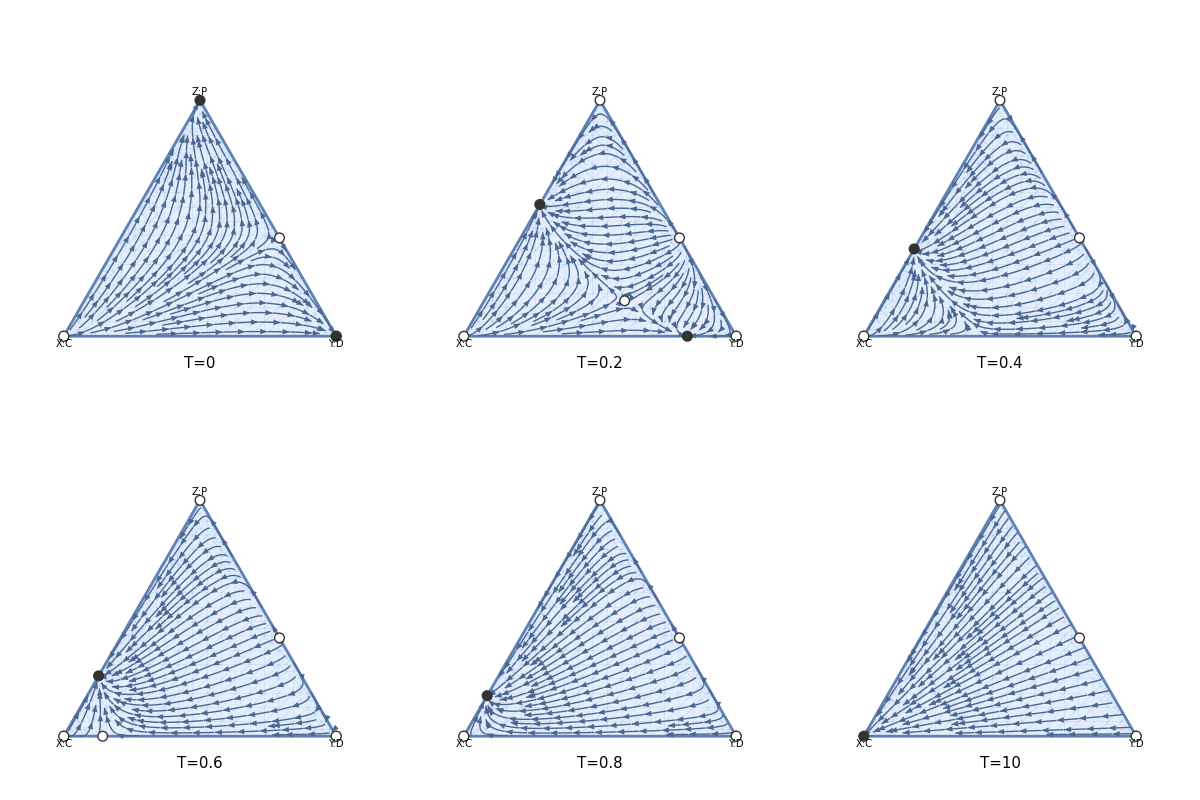

```mathematica
GraphicsGrid[{{plot1,plot2,plot3},{plot4,plot5,plot6}},Spacings->0]
```

#### b

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.1,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.1,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot7=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["b=0.1",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.3,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.3,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot8=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["b=0.3",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.5,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.5,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot9=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["b=0.5",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->10,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->10,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot10=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["b=10",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

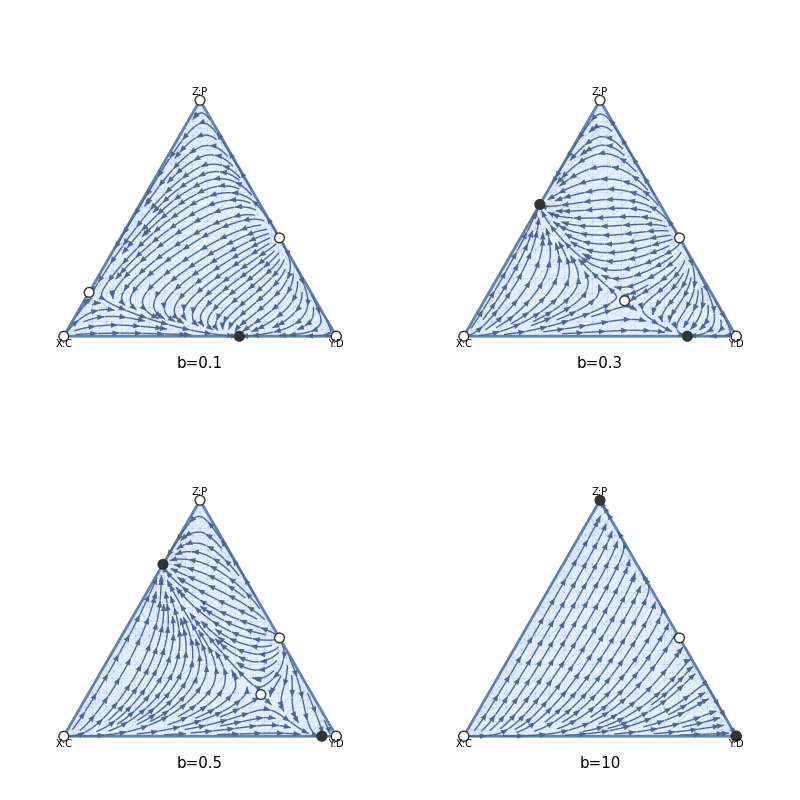

```mathematica
GraphicsGrid[{{plot7,plot8},{plot9,plot10}},Spacings->0]
```

#### β

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.3,β->0.05};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.3,β->0.1};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot1=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["β=0.1",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.3,β->0.3};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.3,β->0.3};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot2=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["β=0.3",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
re={re1, re2,re3};
A3=D[re,{{x,y,z}}]//Simplify;
fixedPoints={};
AppendTo[fixedPoints,{1,0,0}];
AppendTo[fixedPoints,{0,1,0}];
AppendTo[fixedPoints,{0,0,1}];
i=0.055;
RE=.;
RE [x_,y_,z_]=re /.{n1->(n-1) x,n2->(n-1) y,n3->(n-1) z} /. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.3,β->0.5};
NRE=RE[x,y,z];

fixedPoints1={x,y,z}/.Solve[NRE[[2]]==0&&NRE[[1]]==0&&x+y+z==1&&x≥0&&y≥0&&z≥0];
AppendTo[fixedPoints,#]&/@fixedPoints1;
A3n=A3/. {x->x,y->y,z->z,n->5,r->3,c->1,T->0.2,M->0.5,b->0.3,β->0.5};
filed[{x_,y_}]=SimplexTransform[(RE @@( SimplexTransformI[{x,y}]))] {1,1} ;
listVectorOnEdge={#, filed@@#}&/@Flatten[{Table[{0.,y},{y,0.03,1-0.01,i}],Table[{1,y},{y,0.03,1-0.01,i}],Table[{y,0.},{y,0.03,1-0.01,i}],Table[{y,1},{y,0.03,1-0.01,i}]},1];
plot3=Show[StreamPlot[filed[{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},RegionMember[Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],{x,y}]],StreamPoints->Fine,StreamColorFunction->None,StreamStyle->None,Frame->False],
(*ListVectorPlot[{listVectorOnEdge},VectorPoints->All,VectorSizes->0.4,VectorScaling->None],*)
Graphics[{Text[Style["X:C",Italic,FontSize->10],{0.0,-0.03}],Text[Style["Z:P",Italic,FontSize->10],{0.5,(√3)/2+0.03}],Text[Style["Y:D",Italic,FontSize->10],{1.0,-0.03}]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.02],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Stable3Q[#,A3n]&])]}],
Graphics[{RGBColor[.2,.2,.2],PointSize[.020],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{RGBColor[1,1,1],PointSize[.015],Splice[Point/@(SimplexTransform@#&/@Select[fixedPoints,Not[Stable3Q[#,A3n]]&])]}],
Graphics[{Text[Style["β=0.5",Italic,15],{0.5,-0.1}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}}
];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

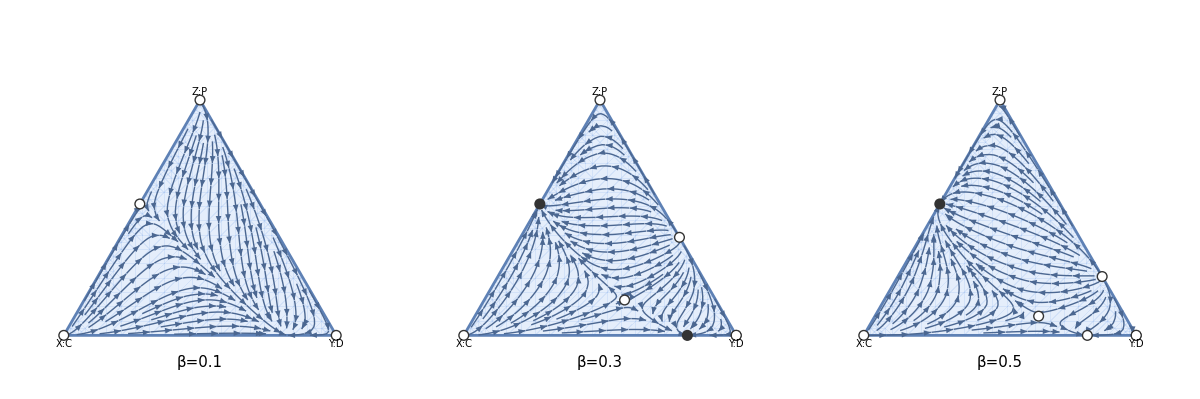

```mathematica
GraphicsRow[{plot1,plot2,plot3},(*自动填满宽度*)Spacings->0]
```